```mathematica
m={{a, b},{c, d}}
```

```mathematica
m
```

```mathematica
B=({{a, b}, {c, d}})
```

```mathematica
CC=({{e, f}, {g, h}})
```

```mathematica
Matrix
```

```mathematica
MatrixForm[B.CC]
```

```mathematica
MatrixForm[-CC.B]
```

```mathematica
MatrixForm[B.CC == -CC.B]
```

```mathematica
Reduce[{{a e+b g,a f+b h},{c e+d g,c f+d h}}=={{-a e-c f,-b e-d f},{-a g-c h,-b g-d h}}]
```

FindRoot::nveq: The number of equations does not match the number of variables in FindRoot[{{a e+b g,a f+b h},{c e+d g,c f+d h}}=={{-a e-c f,-b e-d f},{-a g-c h,-b g-d h}},{{a,1},{b,2},{c,3},{d,4},{e,5},{f,6},{g,7},{h,8}}].

General::stop: Further output of NSolve::infsolns will be suppressed during this calculation.

```mathematica
M=({{r, s}, {t, v}})
```

```mathematica
MatrixForm[M.M]
```

```mathematica
({{r^2+s t, r s+s v}, {r t+t v, s t+v^2}})=0
```

Set::shape: Lists {{r^2+s t,r s+s v},{r t+t v,s t+v^2}} and 0 are not the same shape.

0

```mathematica
Road = ({{200, -400, -a, c}, {a, 300, -b, -d}, {b, -200, -100, e}, {-400, -c, f, 500}, {-f, d, g, -300}, {-g, -e, 200, 200}})
```

```mathematica
vec=({{0}, {0}, {0}, {0}, {0}, {0}})
```

```mathematica
LinearSolve[Road, vec]
```

```mathematica
MatrixForm[{{0},{0},{0},{0}}]
```

```mathematica
Covariance[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1},{0,0,0,0},{0,0,0,0}}]
```

```mathematica
MatrixForm[%]
```

```mathematica
MatrixForm[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1},{0,0,0,0},{0,0,0,0}}]
```

```mathematica
MatrixPlot[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1},{0,0,0,0},{0,0,0,0}}]
```

```mathematica
MatrixForm[%]
```

```mathematica
Road = ({{200+c, -400-a}, {300+a, -b-d}, {b+e, -200-100}, {500+f, -400-c}, {d+g, -300-f}, {200+200, -g-e}})
```

```mathematica
LinearSolve[Road, vec]
```

```mathematica
Grid[{{1,0},{0,1},{0,0},{0,0},{0,0},{0,0}}]
```

```mathematica
Insert[Grid[{{1,0},{0,1},{0,0},{0,0},{0,0},{0,0}}],{Dividers->All,Spacings->1.5 {1,1}},2]
```

```mathematica
B=({{a, b}, {c, d}})
```

```mathematica
C=({{e, f}, {g, h}})
```

```mathematica
S=({{e, f}, {g, h}})
```

```mathematica
B.S
```

```mathematica
B.S//MatrixForm
```

(a e+b g | a f+b h
c e+d g | c f+d h)

```mathematica
-S.B//MatrixForm
```

(-a e-c f | -b e-d f
-a g-c h | -b g-d h)

```mathematica
Solve[B.S == -S.B, {a, b ,c, d, e, f, g, h}]
```

{}

```mathematica
Solve[a e+b g ==-a e-c f && a f+b h == -b e-d f && c e+d g == -a g-c h && c f+d h == -b g-d h , {a, b ,c, d, e, f, g, h}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→-d,e→(c f+b g)/(2 d),h→(-c f-b g)/(2 d)},{a→-d,b→0,e→(c f)/(2 d),h→-(c f)/(2 d)},{a→0,b→0,c→0,d→0},{e→0,f→0,g→0,h→0},{a→0,d→0,g→-(c f)/b,h→-e},{a→(b c)/d,e→-(d f)/b,g→(c f)/b,h→-(c f)/d},{a→-d,e→(c f)/d,g→(c f)/b,h→-(c f)/d},{a→-d,b→0,c→0,e→0,h→0},{a→0,b→0,c→0,d→0,f→0},{a→0,b→0,e→-(d g)/c,f→0,h→0},{a→-d,b→0,e→0,f→0,h→0},{a→0,b→0,d→0,f→0,h→-e},{b→0,d→0,e→0,f→0,h→-(a g)/c},{b→0,e→0,f→0,g→0,h→0},{c→0,e→0,f→0,g→0,h→0},{a→0,c→0,e→-(d f)/b,g→0,h→0},{a→0,c→0,d→0,g→0,h→-e},{c→0,d→0,e→0,g→0,h→-(a f)/b},{a→0,e→0,f→0,g→0,h→0},{a→0,d→0,f→0,g→0,h→-e},{a→-d,b→0,c→0,e→0,f→0,h→0},{a→0,b→0,c→0,f→0,g→0,h→0},{a→0,b→0,c→0,d→0,f→0,g→0},{b→0,c→0,d→0,e→0,f→0,g→0},{b→0,c→0,e→0,f→0,g→0,h→0},{a→0,b→0,e→0,f→0,g→0,h→0},{a→0,b→0,d→0,f→0,g→0,h→-e},{a→0,c→0,e→0,f→0,g→0,h→0},{a→0,c→0,d→0,f→0,g→0,h→-e}}

```mathematica
V=({{1, 1}, {1, -1}})
```

{{1,1},{1,-1}}

```mathematica
W=({{-1, 1}, {1, 1}})
```

{{-1,1},{1,1}}

```mathematica
V.W//MatrixForm
```

(0 | 2
-2 | 0)

```mathematica
-W.V//MatrixForm
```

(0 | 2
-2 | 0)

```mathematica
M=({{r, s}, {t, v}})
```

{{r,s},{t,v}}

```mathematica
N=M.M
```

Set::wrsym: Symbol N is Protected.

{{r^2+s t,r s+s v},{r t+t v,s t+v^2}}

```mathematica
L=M.M
```

{{r^2+s t,r s+s v},{r t+t v,s t+v^2}}

```mathematica
MatrixForm[L]
```

(r^2+s t | r s+s v
r t+t v | s t+v^2)

```mathematica
Vect({{0}, {0}})
```

{{0},{0}}

```mathematica
LinearSolve[L, Vect]//MatrixForm
```

LinearSolve[{{r^2+s t,r s+s v},{r t+t v,s t+v^2}},Vect]

```mathematica
LinearSolve[L, 0]
```

LinearSolve::matrix: Argument 0 at position 2 is not a non-empty rectangular matrix.

LinearSolve[{{r^2+s t,r s+s v},{r t+t v,s t+v^2}},0]

```mathematica
clear [a, b, c, d]
```

clear[a,b,c,d]

```mathematica
X=({{a, b}, {c, d}})
```

{{a,b},{c,d}}

```mathematica
Y=({{e, f}, {g, h}})
```

{{e,f},{g,h}}

```mathematica
X+Y//MatrixForm
```

(a+e | b+f
c+g | d+h)

```mathematica
Solve[(a+e)(d+h)-(c+g)(b+f)==0, {a, b, c, d, e, f, g, h}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{h→(b c-a d-d e+c f+b g+f g)/(a+e)},{e→-a,f→-b},{e→-a,g→-c}}

```mathematica
Solve[{(a+e)(d+h)-(c+g)(b+f)≠0 && ad-cb==0 && eh-gf==0}, {a, b, c, d, e, f, g, h}]
```

```mathematica
Solve[{(a+e)(d+h)-(c+g)(b+f)≠0 && a*d-c*b==0 && e*h-g*f==0}, {a, b, c, d, e, f, g, h}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{d→(b c)/a,h→(f g)/e},{a→0,b→0,h→(f g)/e},{a→0,c→0,h→(f g)/e},{d→(b c)/a,e→0,g→0},{d→(b c)/a,e→0,f→0},{a→0,b→0,e→0,g→0},{a→0,c→0,e→0,f→0}}

```mathematica
Clear[a, b, c, d, e, f, g, h]
```

```mathematica
B=({{a, b}, {c, d}})
```

{{a,b},{c,d}}

```mathematica
S=({{e, f}, {g, h}})
```

{{e,f},{g,h}}

```mathematica
keyword = ({{7, 8}, {11, 11}})
```

{{7,8},{11,11}}

```mathematica
msg1 = ({{19}, {4}})
```

{{19},{4}}

```mathematica
keyword.msg1//MatrixForm
```

(165
253)

```mathematica
good = keyword.msg1//MatrixForm
```

(165
253)

```mathematica
mod[good]
```

mod[(165
253)]

```mathematica
mod[165, 26]
```

mod[165,26]

```mathematica
Mod[good]
```

Mod::argtu: Mod called with 1 argument; 2 or 3 arguments are expected.

Mod[(165
253)]

```mathematica
Mod[good, 26]
```

```mathematica
Mod[({{165}, {253}}),26]
```

{{9},{19}}

```mathematica
Sys = ({{11, -8}, {-11, 7}})
```

{{11,-8},{-11,7}}

```mathematica
Mod[Sys, 26]//MatrixForm
```

(11 | 18
15 | 7)

```mathematica
Det[Sys]
```

-11

```mathematica
Road = ({{200, -400, -a, c}, {a, 300, -b, -d}, {b, -200, -100, e}, {-400, -c, f, 500}, {-f, d, g, -300}, {-g, -e, 200, 200}})
```

{{200,-400,-a,c},{a,300,-b,-d},{b,-200,-100,e},{-400,-c,f,500},{-f,d,g,-300},{-g,-e,200,200}}

```mathematica
V=({{0}, {0}, {0}, {0}, {0}, {0}})
```

{{0},{0},{0},{0},{0},{0}}

```mathematica
Solve[Road == V, {a, b, c, d, e, f, g}]
```

{}

```mathematica
Road01 = ({{-1, 0, 1, 0, 0, 0, 0}, {1, -1, 0, -1, 0, 0, 0}, {0, 1, 0, 0, 1, 0, 0}, {0, 0, -1, 0, 0, 1, 0}, {0, 0, 0, 1, 0, -1, 1}, {0, 0, 0, 0, -1, 0, -1}})
```

{{-1,0,1,0,0,0,0},{1,-1,0,-1,0,0,0},{0,1,0,0,1,0,0},{0,0,-1,0,0,1,0},{0,0,0,1,0,-1,1},{0,0,0,0,-1,0,-1}}

```mathematica
Cars =({{200}, {-300}, {300}, {-100}, {300}, {-400}})
```

{{200},{-300},{300},{-100},{300},{-400}}

```mathematica
LinearSolve[Road01, Cars]
```

{{-100},{-100},{100},{300},{400},{0},{0}}

```mathematica
RowReduce[Road01]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | -1 | 0
0 | 1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 1 | 0 | 0 | -1 | 0
0 | 0 | 0 | 1 | 0 | -1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
R=({{a, b}, {c, d}})
```

{{a,b},{c,d}}

```mathematica
T=({{e, f}, {g, h}})
```

{{e,f},{g,h}}

```mathematica
R.T//MatrixForm
```

(a e+b g | a f+b h
c e+d g | c f+d h)

```mathematica
-T.R//MatrixForm
```

(-a e-c f | -b e-d f
-a g-c h | -b g-d h)

```mathematica
R.R//MatrixForm
```

(a^2+b c | a b+b d
a c+c d | b c+d^2)

```mathematica
E=({{a, s, d}, {n, f, g}})
```

Set::wrsym: Symbol ⅇ is Protected.

{{a,s,d},{n,f,g}}

```mathematica
G=({{j}, {k}})
```

{{j},{k}}

```mathematica
E.G
```

ⅇ.{{j},{k}}

```mathematica
G.E
```

{{j},{k}}.ⅇ

```mathematica
M=({{a, b}, {c, b}})
```

{{a,b},{c,b}}

```mathematica
M2 = M.M
```

{{a^2+b c,a b+b^2},{a c+b c,b^2+b c}}

```mathematica
Solve[a^2+b c==0 && a b+b^2==0 && a c+b c ==0 && b^2+b c ==0, {a, b, c, d}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→0,b→0},{b→-a,c→a},{a→0,b→0,c→0}}

```mathematica
R=({{2, -2}, {2, 0}})
```

{{2,-2},{2,0}}

```mathematica
R.R
```

{{0,-4},{4,-4}}

```mathematica
Solve[a*a+b*c==0 && a*b+b*b==0 && a*c+b*c ==0 && b*b+b*c ==0, {a, b, c, d}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→0,b→0},{b→-a,c→a},{a→0,b→0,c→0}}

```mathematica
A=({{a, b}, {c, d}})
```

{{a,b},{c,d}}

```mathematica
B=({{e, f}, {g, h}})
```

{{e,f},{g,h}}

```mathematica
A+B//MatrixForm
```

(a+e | b+f
c+g | d+h)

```mathematica
Solve[a*d-b*c ≠ 0 && e*h-f*g ≠ 0 && (a+e)(d+h)-(c+g)(b+f)==0, {a, b, c, d, e, f, g, h}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{h→(b c-a d-d e+c f+b g+f g)/(a+e)},{e→-a,f→-b},{e→-a,g→-c}}

```mathematica
A=({{1, 2}, {3, 4}})
```

{{1,2},{3,4}}

```mathematica
B=({{-1, -2}, {7, 8}})
```

{{-1,-2},{7,8}}

```mathematica
det(A)
```

{{det,2 det},{3 det,4 det}}

```mathematica
Solve[a*d-b*c == 0 && e*h-f*g == 0 && (a+e)(d+h)-(c+g)(b+f)≠ 0, {a, b, c, d, e, f, g, h}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{d→(b c)/a,h→(f g)/e},{a→0,b→0,h→(f g)/e},{a→0,c→0,h→(f g)/e},{d→(b c)/a,e→0,g→0},{d→(b c)/a,e→0,f→0},{a→0,b→0,e→0,g→0},{a→0,c→0,e→0,f→0}}

```mathematica
M=({{s, r}, {t, v}})
```

{{s,r},{t,v}}

```mathematica
M.M//MatrixForm
```

(s^2+r t | r s+r v
s t+t v | r t+v^2)

```mathematica
Solve[r ≠0 &&s ≠0 &&t ≠0 &&v ≠0 && s*s+r*t==0 &&r*s+r*v==0 &&s*t+t*v==0 &&r*t+v*v==0 , {r, s, t, v}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{t→-s^2/r,v→-s}}

```mathematica
U=({{-4, 2}, {-8, 4}})
```

{{-4,2},{-8,4}}

```mathematica
U.U
```

{{0,0},{0,0}}

```mathematica
FCB=({{-1, 0, 1, 0, 0, 0, 0}, {1, -1, 0, -1, 0, 0, 0}, {0, 1, 0, 0, 1, 0, 0}, {0, 0, -1, 0, 0, 1, 0}, {0, 0, 0, 1, 0, -1, 1}, {0, 0, 0, 0, -1, 0, -1}})
```

{{-1,0,1,0,0,0,0},{1,-1,0,-1,0,0,0},{0,1,0,0,1,0,0},{0,0,-1,0,0,1,0},{0,0,0,1,0,-1,1},{0,0,0,0,-1,0,-1}}

```mathematica
road={{a},{b},{c},{d},{e},{f},{g}}
```

{{a},{b},{c},{d},{e},{f},{g}}

```mathematica
cars={{200},{-300},{300},{-100},{300},{-400}}
```

{{200},{-300},{300},{-100},{300},{-400}}

```mathematica
Solve[FCB.road == cars, {a, b, c ,d, e, f, g}]
```

{{c→200+a,d→300+a-b,e→300-b,f→100+a,g→100+b}}

```mathematica
{{c->200+a,d->900+a-b,e->600-b,f->200+a,g->-200+b}}
```

{{c→200+a,d→900+a-b,e→600-b,f→200+a,g→-200+b}}

```mathematica
fcb =RowReduce[FCB]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | -1 | 0
0 | 1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 1 | 0 | 0 | -1 | 0
0 | 0 | 0 | 1 | 0 | -1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
road=({{a}, {b}, {c}, {d}, {e}, {f}, {g}})
```

{{a},{b},{c},{d},{e},{f},{g}}

```mathematica
cars=({{200}, {-300}, {300}, {-100}, {300}, {-400}})
```

{{200},{-300},{300},{-100},{300},{-400}}

```mathematica
c
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c→200+a,d→300+a-b,e→300-b,f→100+a,g→100+b}}

```mathematica
Flatten[{c,d,e,f,g}/.Solve[FCB.road == cars && a ≠ 0 &&b ≠ 0 &&c ≠ 0 &&d ≠ 0 &&e ≠ 0 &&f ≠ 0 &&g ≠ 0, {a, b, c ,d, e, f, g}]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{200+a,300+a-b,300-b,100+a,100+b}

```mathematica
Subsets[Sort[{200+a,300+a-b,300-b,100+a,100+b}]]
```

{{},{100+a},{200+a},{300-b},{300+a-b},{100+b},{100+a,200+a},{100+a,300-b},{100+a,300+a-b},{100+a,100+b},{200+a,300-b},{200+a,300+a-b},{200+a,100+b},{300-b,300+a-b},{300-b,100+b},{300+a-b,100+b},{100+a,200+a,300-b},{100+a,200+a,300+a-b},{100+a,200+a,100+b},{100+a,300-b,300+a-b},{100+a,300-b,100+b},{100+a,300+a-b,100+b},{200+a,300-b,300+a-b},{200+a,300-b,100+b},{200+a,300+a-b,100+b},{300-b,300+a-b,100+b},{100+a,200+a,300-b,300+a-b},{100+a,200+a,300-b,100+b},{100+a,200+a,300+a-b,100+b},{100+a,300-b,300+a-b,100+b},{200+a,300-b,300+a-b,100+b},{100+a,200+a,300-b,300+a-b,100+b}}

```mathematica
Flatten[%292]
```

{100+a,200+a,300-b,300+a-b,100+b,100+a,200+a,100+a,300-b,100+a,300+a-b,100+a,100+b,200+a,300-b,200+a,300+a-b,200+a,100+b,300-b,300+a-b,300-b,100+b,300+a-b,100+b,100+a,200+a,300-b,100+a,200+a,300+a-b,100+a,200+a,100+b,100+a,300-b,300+a-b,100+a,300-b,100+b,100+a,300+a-b,100+b,200+a,300-b,300+a-b,200+a,300-b,100+b,200+a,300+a-b,100+b,300-b,300+a-b,100+b,100+a,200+a,300-b,300+a-b,100+a,200+a,300-b,100+b,100+a,200+a,300+a-b,100+b,100+a,300-b,300+a-b,100+b,200+a,300-b,300+a-b,100+b,100+a,200+a,300-b,300+a-b,100+b}

```mathematica
Tally[%293]
```

{{100+a,16},{200+a,16},{300-b,16},{300+a-b,16},{100+b,16}}

```mathematica
Normal[CoefficientArrays[{200+a,300+a-b,300-b,100+a,100+b},{a,b}]⟦2⟧]
```

{{1,0},{1,-1},{0,-1},{1,0},{0,1}}

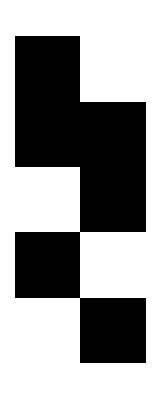

```mathematica
ArrayPlot[{{1,0},{1,-1},{0,-1},{1,0},{0,1}}]
```

```mathematica
TableForm[{{-100},{-100},{100},{300},{400},{0},{0}}]
```

-100
-100
100
300
400
0
0

```mathematica
Flatten[{{-100},{-100},{100},{300},{400},{0},{0}}]
```

{-100,-100,100,300,400,0,0}

```mathematica
Normalize[{-100,-100,100,300,400,0,0}]
```

{-1/(2 √7),-1/(2 √7),1/(2 √7),3/(2 √7),2/(√7),0,0}

```mathematica
keyword=({{7, 8}, {11, 11}})
```

{{7,8},{11,11}}

```mathematica
msg1=({{19}, {4}})
```

{{19},{4}}

```mathematica
Mod[keyword.msg1,26]
```

{{9},{19}}

```mathematica
Mod[keyword.({{4}, {23}}),26]
```

{{4},{11}}

```mathematica
keyword.({{12}, {4}})
```

{{278},{407}}

```mathematica
Inverse[keyword]//MatrixForm
```

```mathematica
11.({{-1, 8/11}, {1, -7/11}})//MatrixForm
```

(-11. | 8.
11. | -7.)

```mathematica
moddet =Mod[Det[keyword],26]
```

15

```mathematica
redet=ModularInverse[moddet,26]
```

7

```mathematica
adj[m_]:=Inverse[m] Det[m]
```

```mathematica
adj[keyword]
```

{{11,-8},{-11,7}}

```mathematica
adjmod =Mod[adj[keyword],26]//MatrixForm
```

(11 | 18
15 | 7)

```mathematica
decrypkey = Mod[7*{{11,18},{15,7}},26]//MatrixForm
```

(25 | 22
1 | 23)

```mathematica
decrypkey={{25,22},{1,23}}
```

{{25,22},{1,23}}

```mathematica
decry[x_]:=Mod[decrypkey.x,26]//MatrixForm
```

```mathematica
ltr[y_,z_]:=({{LetterNumber[y]-1}, {LetterNumber[z]-1}})
```

```mathematica
decry[ltr["N", "N"]]
```

(13
0)

```mathematica
decry[ltr["Z", "J"]]
```

(17
24)

```mathematica
decry[ltr["H", "R"]]
```

(3
8)

```mathematica
bltr[{1,3,8,9,5,22, 9,14,7,5,24,20, 18, 1, 15, 18, 4, 9, 14, 1, 18, 25}]
```

ACHIEVINGEXTRAORDINARY

```mathematica
”QWJJOP EXWGBU PFADHR NNZJ”.
```

(18
18)

(0
6)

(4
24)

```mathematica
bltr[{x_}]:=FromCharacterCode[x]
```

```mathematica
bltr[{20, 5, 19, 20, 13, 5, 19, 19, 1, 7, 5, 24}]
```

TESTMESSAGEX

```mathematica
FromCharacterCode[70]
```

F

bltr[9,19]

{65}

```mathematica
decry[9]
```

Mod[9.{{25,22},{1,23}},26]

```mathematica
FCB=({{-1, 0, 1, 0, 0, 0, 0}, {1, -1, 0, -1, 0, 0, 0}, {0, 1, 0, 0, 1, 0, 0}, {0, 0, -1, 0, 0, 1, 0}, {0, 0, 0, 1, 0, -1, 1}, {0, 0, 0, 0, -1, 0, -1}})
```

{{-1,0,1,0,0,0,0},{1,-1,0,-1,0,0,0},{0,1,0,0,1,0,0},{0,0,-1,0,0,1,0},{0,0,0,1,0,-1,1},{0,0,0,0,-1,0,-1}}

```mathematica
cars=({{200}, {-900}, {600}, {0}, {500}, {-400}})
```

{{200},{-900},{600},{0},{500},{-400}}

```mathematica
road=({{a}, {b}, {c}, {d}, {e}, {f}, {g}})
```

{{a},{b},{c},{d},{e},{f},{g}}

```mathematica
Solve[FCB.road == cars && a ≠ 0 &&b ==  300 &&c ≠ 0 &&d ≠ 0 &&e ≠ 0 &&f ≠ 0 &&g ≠ 0, {a, b, c ,d, e, f, g}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b→300,c→200+a,d→600+a,e→300,f→200+a,g→100}}

```mathematica
First[{{b->300,c->200+a,d->600+a,e->300,f->200+a,g->100}}]
```

{b→300,c→200+a,d→600+a,e→300,f→200+a,g→100}

```mathematica
{b->300,c->200+a,d->600+a,e->300,f->200+a,g->100}/.Rule->Equal
```

{b==300,c==200+a,d==600+a,e==300,f==200+a,g==100}

```mathematica
Solve[{b==300,c==200+a,d==600+a,e==300,f==200+a,g==100},{a,b,c,d,e,f,g}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b→300,c→200+a,d→600+a,e→300,f→200+a,g→100}}

```mathematica
First[{{b->300,c->200+a,d->600+a,e->300,f->200+a,g->100}}]
```

{b→300,c→200+a,d→600+a,e→300,f→200+a,g→100}

```mathematica
{b,c,d,e,f,g}/.{{b->300,c->200+a,d->600+a,e->300,f->200+a,g->100}}
```

{{300,200+a,600+a,300,200+a,100}}

```mathematica
Grid[{{300,200+a,600+a,300,200+a,100}}]
```

300 | 200+a | 600+a | 300 | 200+a | 100

```mathematica
Insert[Grid[{{300,200+a,600+a,300,200+a,100}}],{Dividers->All,Spacings->1.5 {1,1}},2]
```

300 | 200+a | 600+a | 300 | 200+a | 100

```mathematica
Insert[Grid[{{300,200+a,600+a,300,200+a,100}},{Dividers->All,Spacings->{1.5,1.5}}],{Dividers->All,Spacings->1.5 {1,1}},2]
```

300 | 200+a | 600+a | 300 | 200+a | 100

Thread::tdlen: Objects of unequal length in {9} {25,22} cannot be combined.

Thread::tdlen: Objects of unequal length in {19} {1,23} cannot be combined.

```mathematica
Solve[200-400-a+c==0 &&a+300-b-d==0 && b-200-100+e==0 && -400-c+f+500==0 &&-f+d+g-300==0 &&-g-e+200+200==0,{a, b, c, d, e, f, g}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c→200+a,d→300+a-b,e→300-b,f→100+a,g→100+b}}